```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/12279703.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
eig = Flatten[Map[Eigenvalues, cmatdata[[All, 2;;]], {2}]];
```

```mathematica
α = 31.12629007164102/η;
```

```mathematica
randmat = Partition[(# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√(α $N)), $N], Length[data]*$K], $K];
```

```mathematica
randeig = Flatten[Map[Eigenvalues, randmat, {2}]];
```

```mathematica
fig[1] = Histogram[{eig, randeig}, 350, PDF,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\lambda", "\\rho"},
FrameTicks->{{With[{ticks=0.0+0.5Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=-0.4+0.2Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ChartLegends->Placed[MaTeX/@{"\\text{simulation}", "\\text{traceless GUE}"}, {Bottom, Bottom}],
PlotRange->All,
ImageSize->14cm
];
```

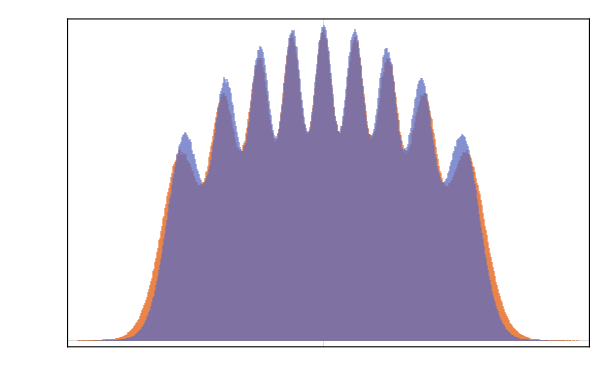

```mathematica
Magnify[fig[1], 1]
```

```mathematica
Export[plotsDir<>"/5-eig-dist.pdf", fig[1]]
```

../../../plots/plots-thesis/5-eig-dist.pdf

```mathematica
rad = radius/@data;
```

```mathematica
radrand = Table[Total[Tr[#.#]&/@randmat[[k, All]]]//Chop, {k, 1, Length[randmat]}];
```

```mathematica
rad[[3, 2]]
```

4.3414

```mathematica
radrand[[2]]
```

1.21443+0. ⅈ

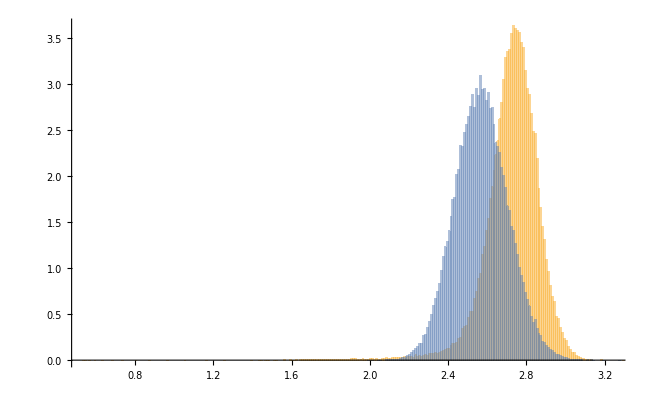

```mathematica
Histogram[{rad[[All, 2]], radrand}, 350, PDF]
```

```mathematica
trX5sq = Sum[Tr[#.#]&/@cmatdata[[All, A+1]]//Chop, {A,5, 5}];
```

```mathematica
trX1sq = Sum[Tr[#.#]&/@cmatdata[[All, A+1]]//Chop, {A, 1, 1}];
```

```mathematica
trX1sqrand =Sum[ Tr[#.#]&/@randmat[[All, A]]//Chop, {A, 1, 1}];
```

```mathematica
Mean[trX1sq]
```

0.303201

```mathematica
Mean[trX1sqrand]
```

0.28555

```mathematica
Entropy
```

```mathematica
trX1X2 = Tr[#[[2]].#[[3]]]&/@cmatdata//Chop;
trX1X2rand = Tr[#[[1]].#[[2]]]&/@randmat//Chop;
```

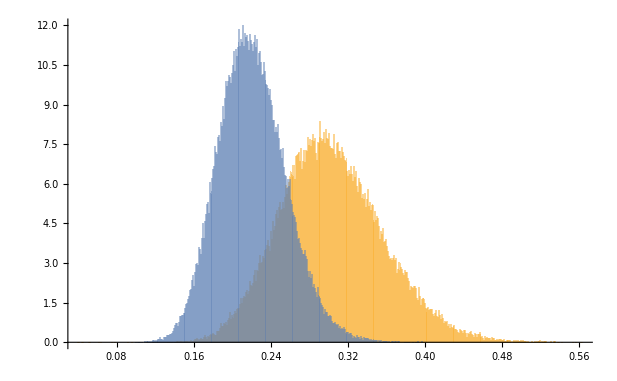

```mathematica
Histogram[{trX1sq, trX1sqrand}, 450, PDF]
```

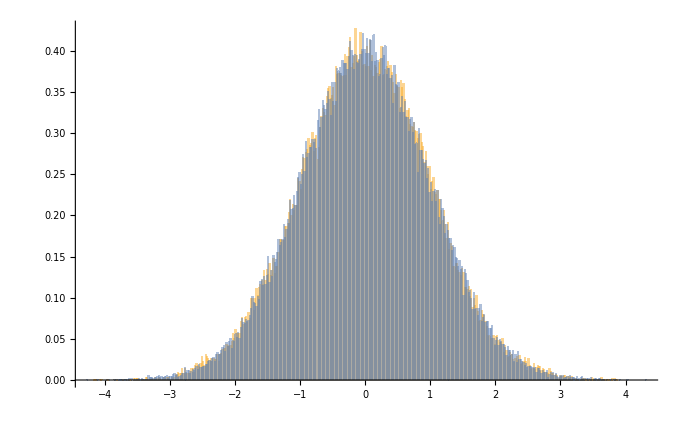

```mathematica
Histogram[{Standardize[trX1X2], Standardize[trX1X2rand]}, 350, PDF]
```

```mathematica
η =(StandardDeviation[trX1sq]/StandardDeviation[trX1sqrand])^2
```

1.37161

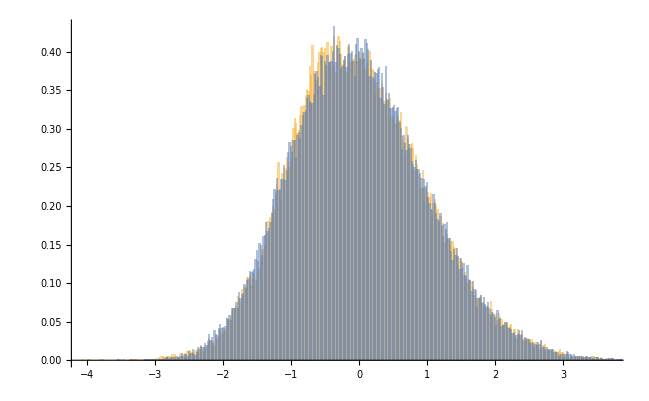

```mathematica
Histogram[{Standardize[trX1sq], Standardize[trX1sqrand]}, 350, PDF]
```

```mathematica
Covariance[trX1sq, trX2sq]
```

-0.0000421786

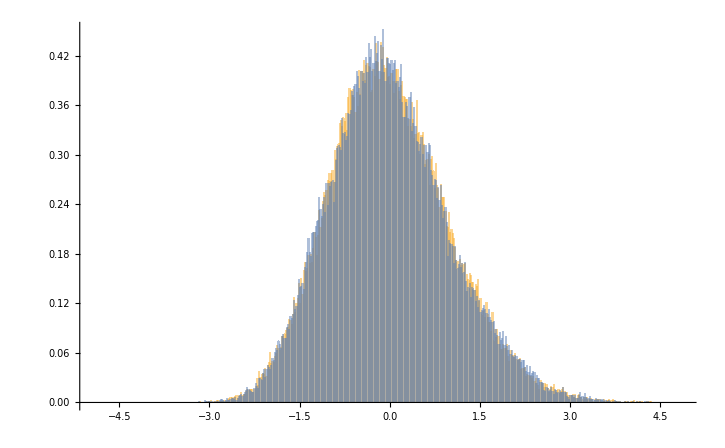

```mathematica
Histogram[{Standardize[trX1sq], Standardize[trX5sq]}, 450, PDF]
```

```mathematica
η = (StandardDeviation[cmatdata[[All, 2, 1, 1]]]/StandardDeviation[randmat[[All, 2, 1, 1]]])^2
```

0.773066

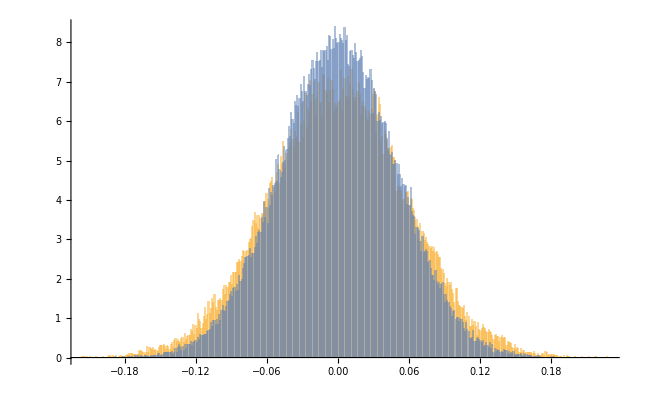

```mathematica
Histogram[{cmatdata[[All, 2, 1, 1]]//Chop, randmat[[All, 2, 1, 1]]//Chop}, 450, PDF]
```

```mathematica
Covariance[cmatdata[[All, 2, 1, 1]]]
```

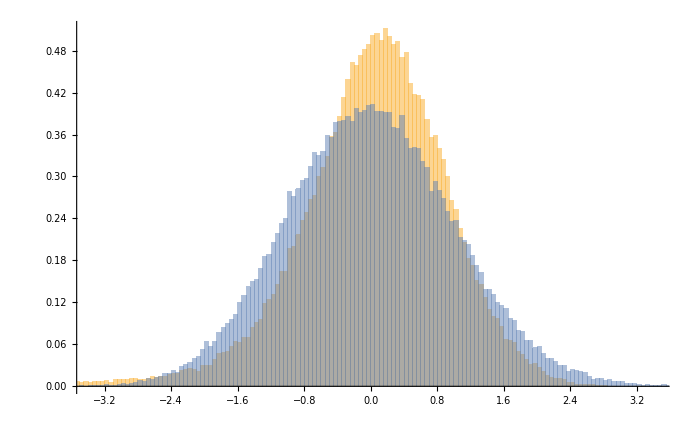

```mathematica
Histogram[{Standardize[trX1sq], Standardize[trX1sqrand]}, 550, PDF]
```